```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"];
<<MaTeX`;
MaTeX["x^2"] (*Este bloque echa a andar MaTeX. Para tener tipografia tipo LaTeX*)
```

-Graphics-

```mathematica
(*Parametros*)
ν=1/3;
a = 0.01;
aPrime = 0.01;
```

```mathematica
coeficienteB[ω_, k_]:=-(ω+(1-ν)k^2 Cosh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Cos[(√(ω+k^2))/2])*a;
coeficienteBPrima[ω_, k_]:=-(ω+(1-ν)k^2 Sinh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Sin[(√(ω+k^2))/2])*aPrime;
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
```

```mathematica
amplitudWSim[k_,y_]:=a*Cosh[√(frecuenciaωSimPositivo[k, 0]+k^2)*y]+coeficienteB[frecuenciaωSimPositivo[k, 0],k]*Cos[√(frecuenciaωSimPositivo[k, 0]-k^2)*y];
amplitudWAntiSim[k_,y_]:=aPrime*Sinh[√(2*k^2)*y];
```

```mathematica
DisplacementSim[k_,x_,y_,t_]:=Re[amplitudWSim[k,y]*Exp[I*(k*x-frecuenciaωSimPositivo[k, 0]*t)]];
DisplacementAntiSim[k_,x_,y_,t_]:=Re[amplitudWAntiSim[k,y]*Exp[I*(k*x-k^2*t)]];
```

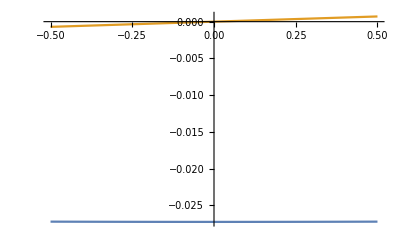

```mathematica
Plot[{DisplacementSim[0.1,0.0,y,0.0], DisplacementAntiSim[0.1,0.0,y,0.0]},{y,-0.5,0.5}, PlotRange->All]
```

```mathematica
Manipulate[Plot3D[DisplacementSim[0.1,x,y,t], {x,-50,50},{y,-0.5,0.5}],{t,0.0, 100.0}]
```

```mathematica
Manipulate[Plot3D[DisplacementAntiSim[0.1,x,y,t], {x,-10,10},{y,-0.5,0.5}],{t,0.0, 1000.0}]
```